# 2. domača naloga

## 1. naloga

a)  Definirajte funkcijo , ki sprejme naravni števili  in  in vrne matriko dimenzije , kjer se na vsakem mestu v matriki pojavi vsota indeksa stolpca in indeksa vrstice.
b) Izračunajte lastne vrednosti in lastne vektorje matrike .
c)  Narišite lastne vektorje matrike .
d) Izračunajte karakteristični polinom matrike .
e) Matriko  diagonalizirajte. Določite ustrezno diagonalno matriko , prehodno matriko  in .
f) Rešite matrično enačbo .

```mathematica
A[n_,m_]:=Table[i+j,{i,1,n},{j,1,m}]
A[3,3]
```

{{2,3,4},{3,4,5},{4,5,6}}

```mathematica
mat=A[3,3];
Eigenvalues[mat]
Eigenvectors[mat]
```

{6+√42,6-√42,0}

{{-(-17-2 √42)/(23+4 √42),-(-20-3 √42)/(23+4 √42),1},{-(17-2 √42)/(-23+4 √42),-(20-3 √42)/(-23+4 √42),1},{1,-2,1}}

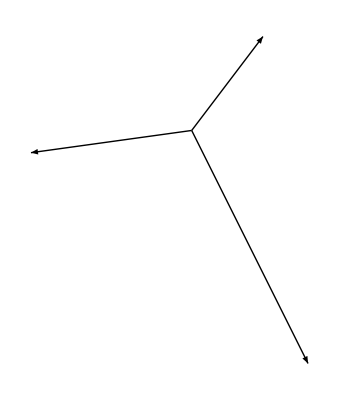

```mathematica
vecs=Eigenvectors[mat];
Graphics[Table[Arrow[{{0,0},Take[vecs[[i]],2]}],{i,Length[vecs]}]]
```

```mathematica
CharacteristicPolynomial[mat,λ]
```

6 λ+12 λ^2-λ^3

```mathematica
{vals,vecs}=Eigensystem[mat];
G=DiagonalMatrix[vals];
P=Transpose[vecs];
PInv=Inverse[P];
Simplify[P.G.PInv]
```

{{2,3,4},{3,4,5},{4,5,6}}

```mathematica
X=Array[x,{3,3}]; 
eq=mat.X+P.X==G.X+IdentityMatrix[3];
sol=Solve[Flatten[eq],Flatten[X]]
```

{{x[1,1]→-(-97+21 √42)/(3 (-27+26 √42)),x[1,2]→-((-4+√42) (23+4 √42))/(6 (-27+26 √42)),x[1,3]→-(106-33 √42)/(6 (-27+26 √42)),x[2,1]→((-23+4 √42) (17179+2683 √42))/(66 (-4+√42) (23+4 √42) (-27+26 √42)),x[2,2]→((-23+4 √42) (2276+359 √42))/(132 (-27+26 √42)),x[2,3]→-((-23+4 √42) (71954+11177 √42))/(66 (-4+√42) (23+4 √42) (-27+26 √42)),x[3,1]→-(3023-382 √42)/(3 (-4+√42) (23+4 √42) (-27+26 √42)),x[3,2]→-(2 (64+7 √42))/(3 (-27+26 √42)),x[3,3]→-(-10489-1333 √42)/(3 (-4+√42) (23+4 √42) (-27+26 √42))}}

## 2. naloga

Imamo klančino z naklonom 30 stopinj dolžine 10m. Na dnu klančine se nahaja ravnina dolžine 10m. Na levem in desnem robu se nahaja stena (glej sliko). 
Kroglico z radijem 10cm spustimo na vrhu klanca, da se začne gibati pod vplivom gravitacije. Predpostavite lahko, da med kroglico in podlago ni trenja in 
da se zaradi kotaljenja energija ne izgublja. Ko pride kroglica na dno klanca, se giblje v vodoravni smeri z enako velikim vektorjem hitrosti (predpostavi, 
da je kot dovolj majhen, da na pride do odboja). 
Simulirajte kotaljenje kroglice po klančini in ravnini, ki se odbija od desnega roba.
Za gravitacijski pospešek vzemite g = 9.81, začetna hitrost kroglice naj bo v0 = 0.

a) Definiraj gravitacijski pospešek, naklon, dolžino klanca, začetno hitrost in radij kroglice.

b) Nariši klančino, tla in obe steni.

c) Na sliko dodaj kroglico tako, da se bo kroglica premaknila, če se spremeni njeno središče.

d) Definiraj funkcijo `naKlancu`, ki sprejme središče kroglice in vrne `True`, če je kroglica na klancu.

e) Definiraj funkcijo `desniRob`, ki sprejme središče kroglice in vrne `True`, če je kroglica trčila ob desni rob.

f) Definiraj funkcijo `posodobiHitrost`, ki sprejme vektor trenutne hitrost kroglice in kot α ter vrne novo hitrost, gibanja po klančini z naklonom α.

g) Definiraj funkcijo `hitrostNaKlanec`, ki sprejme vektor trenutne hitrosti kroglice in kot α ter vrne novo hitrost, ki jo dobi kroglica, ko iz ravnega dela preide na klanec z naklonom α.

h) Definiraj funkcijo `hitrostSKlanca`, ki sprejme vektor trenutne hitrosti kroglice in vrne novo hitrost, ki jo dobi kroglica, ko s klanca preide na ravni del.

i) S pomočjo prejšnjih funkcij simuliraj premikanje kroglice.

```mathematica
g=9.81; (*gravitaciski pospešek[m/s^2]*)
α=30 Degree; (*naklon klanca*)
Lkl=10; (*dolžina klanca[m]*)
Lr=10; (*dolžina ravnine[m]*)
r=0.1; (*radij krogle[m]*)
v0=0;
```

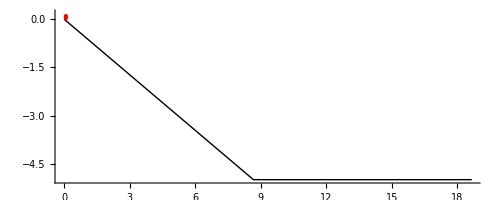

```mathematica
točka1={0,0};
točka2={Lkl*Cos[α],-Lkl*Sin[α]};
točka3={točka2[[1]]+Lr,točka2[[2]]};

(*Risanje poti in začetne krogle*)
Graphics[{Line[{točka1,točka2,točka3}],Red,Disk[točka1+{r*Sin[α],r*Cos[α]},r]},Axes->True,AspectRatio->Automatic]
```

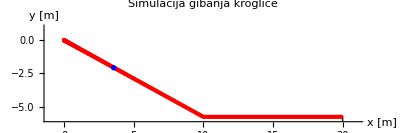

```mathematica
(*Položaj krogle v odvisnosti od časa t*)
(*Numerične vrednosti*)g=9.81;
alpha=30 Degree;
Lklanec=10;
Lravnina=10;

(*Prehodni čas in hitrost*)
t1=Sqrt[2 Lklanec/(g Sin[alpha])];
v1=g Sin[alpha] t1;

(*Položaj*)
x[t_]:=If[t<=t1,0.5 g Sin[alpha] t^2,Lklanec+v1 (t-t1)];
y[t_]:=If[t<=t1,-x[t] Tan[alpha],-Lklanec Tan[alpha]];

(*Trenutni čas*)
tKroglica=1.2; 


trajektorija=Table[{x[t],y[t]},{t,0,t1+Lravnina/v1,0.01}];

(*Slikanje*)
Graphics[{Black,Line[{{0,0},{Lklanec,-Lklanec Tan[alpha]},{Lklanec+Lravnina,-Lklanec Tan[alpha]}}],Dashed,Line[{{Lklanec+Lravnina,-Lklanec Tan[alpha]},{Lklanec+Lravnina,-Lklanec Tan[alpha]-1}}],Red,PointSize[Large],Point/@trajektorija,Blue,Disk[{x[tKroglica],y[tKroglica]},0.2] },Axes->True,AspectRatio->1/3,PlotRange->{{-1,Lklanec+Lravnina+1},{-6,1}},AxesLabel->{"x [m]","y [m]"},PlotLabel->"Simulacija gibanja kroglice"]
```

```mathematica
naKlancu[sredisce_]:=sredisce[[1]]<=Lklanec
```

```mathematica
desniRob[sredisce_]:=sredisce[[1]]>=(Lklanec+Lravnina)
```

```mathematica
posodobiHitrost[v_,kot_]:=v+g {Cos[kot],-Sin[kot]}
```

```mathematica
hitrostNaKlance[v_,alpha_]:=Module[{vnov},vnov=g Sin[alpha] t1;
{vnov Cos[alpha],-vnov Sin[alpha]}]
```

```mathematica
hitrostSKlanca[v_,alpha_]:={Norm[v],0}
```

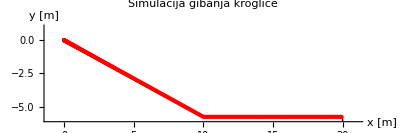

🔁

```mathematica
g=9.81;
alpha=30 Degree;
Lklanec=10;
Lravnina=10;

(*Prehodni čas in hitrost*)
t1=Sqrt[2 Lklanec/(g Sin[alpha])];
v1=g Sin[alpha] t1;

(*Položaj*)
x[t_]:=If[t<=t1,0.5 g Sin[alpha] t^2,Lklanec+v1 (t-t1)];
y[t_]:=If[t<=t1,-x[t] Tan[alpha],-Lklanec Tan[alpha]];
trajektorija=Table[{x[t],y[t]},{t,0,t1+Lravnina/v1,0.01}];

Graphics[{Black,Line[{{0,0},{Lklanec,-Lklanec Tan[alpha]},{Lklanec+Lravnina,-Lklanec Tan[alpha]}}],Dashed,Line[{{Lklanec+Lravnina,-Lklanec Tan[alpha]},{Lklanec+Lravnina,-Lklanec Tan[alpha]-1}}],Red,PointSize[Large],Point/@trajektorija},Axes->True,AspectRatio->1/3,PlotRange->{{-1,Lklanec+Lravnina+1},{-6,1}},AxesLabel->{"x [m]","y [m]"},PlotLabel->"Simulacija gibanja kroglice"]
🔁
```